```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
Needs["PlotLegends`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/analysis-mirror_neutrons/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]];
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Working Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\runs2

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

```mathematica
lineStyle={Thin,Gray,Dashed};
line11=Line[{{0,6000},{16,6000}}];
line12=Line[{{8,2000},{8,-2500}}];
lineStyle2={Thin,Gray,Dashed};
lineStyle3={Thick,Black};
line21=Line[{{8.82,10000},{8.82,-2500}}];
line22=Line[{{7.2,10000},{7.2,-2500}}];
wr=8;wo=8;alpha=.8;
pt1[xx_]:=N[10000(.2+alpha*wr^2/((xx-wo)^2+wr^2)Cos[15.44-7(xx*8/29)]^2)];
pt2[xx_]:=N[10000(1-alpha*wr^2/((xx-wo)^2+wr^2)Cos[15.44-7(xx*8/29)]^2)];
pt3[xx_]:=N[10000(.2+alpha*wr^2/((xx-wo)^2+wr^2))];
pt4[xx_]:=N[10000(1-alpha*wr^2/((xx-wo)^2+wr^2))];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
exp1=Rasterize[Plot[{pt1[xx],pt2[xx],pt3[xx],pt4[xx]},{xx,2,14},Frame->True,Axes->False,PlotRange->Automatic,
Epilog->{
{Directive[lineStyle],line11,line12,Text[Style["N_0",FontSize->Large],{29.3*8/29,6500}],Text[Style["ω_0",FontSize->Large],{8.25,550}]},
{Directive[lineStyle2],line21,line22,{Arrowheads[{-.02,.02}],Arrow[{{7.2,5000},{8.82,5000}}]},Text[Style["1/(2  T)",FontSize->Large],{8,5500}]},
{Directive[lineStyle3],Text[Style["X",FontSize->Medium],{7.65,6500}],Text[Style["X",FontSize->Medium],{7.65,5500}],Text[Style["X",FontSize->Medium],{7.55,5500}],Text[Style["X",FontSize->Medium],{7.55,6500}],(**)Text[Style["X",FontSize->Medium],{8.375,5500}],Text[Style["X",FontSize->Medium],{8.375,6500}],Text[Style["X",FontSize->Medium],{8.475,6500}],Text[Style["X",FontSize->Medium],{8.475,5500}]}
},
FrameLabel->{"ω_n","N(#Neutrons)"},TicksStyle->Directive[FontSize->40],FrameStyle->Thick,LabelStyle->{28,Black,Bold},PlotLegends->{"Spin+","Spin-"},FrameTicks->LinTicks,PlotStyle->{{Blue,Thick},{Red,Thick},{Brown,Dashed,Thick},{Brown,Dashed,Thick}},ImageSize->{1000}],
ImageResolution->100]
```

-Graphics-

## HD-Ramsey Curve

```mathematica
(*
  27: Nup
28: Ndown
-1: f^RF_n
-5: f^RF_Hg
20: f_Hg
21: Err(f_Hg)
-3: nRF-Amlitude (muA)
-8: HgRF-Amplitude (muA)
*)
```

```mathematica
runNum={12676,12677,12678};
i=1;
data1=ReadList[StringJoin[AscDir,"\\","Ramsey-Pattern","\\",IntegerString[runNum[[i]],10,6],"_Meta3.edm"],metaStructure];
i=2;
data2=ReadList[StringJoin[AscDir,"\\","Ramsey-Pattern","\\",IntegerString[runNum[[i]],10,6],"_Meta3.edm"],metaStructure];
i=3;
data3=ReadList[StringJoin[AscDir,"\\","Ramsey-Pattern","\\",IntegerString[runNum[[i]],10,6],"_Meta3.edm"],metaStructure];
data=Join[data1,data2,data3];
maxCy=Dimensions[data][[1]];
```

```mathematica
mult=.000003902;
(*aCy=Round[(maxCy-4)/4];
fita[ftdata_]:=(
nlm=NonlinearModelFit[ftdata,(-bb Cos[((xx-cc)*2Pi)/(180*mult)]),{{bb,.8},{cc,Mean[ftdata[[;;,1]]]}},xx];Return[{{bb/.nlm[[1]][[2]],nlm["ParameterErrors"][[1]]},{cc/.nlm[[1]][[2]],nlm["ParameterErrors"][[2]]}}];
);
fitsa=Table[{{0,0},{0,0}},{k,1,aCy}];
pts=Table[{0,0},{k,1,4}];
aerr=Table[0,{k,1,maxCy-3}];
ptpts={};
Quiet[
For[i=1,i≤maxCy-4,i+=4,
For[j=0,j≤3,j++,
pts[[j+1]]={N[data[[i+j]][[-1]]/data[[i+j]][[-5]]],N[((data[[i+j]][[27]]-data[[i+j]][[28]])/(data[[i+j]][[27]]+data[[i+j]][[28]]))]};
aerr[[i+j]]=(Sqrt[data[[i+j]][[27]]]+Sqrt[data[[i+j]][[28]]])*Sqrt[2]/(data[[i+j]][[27]]+data[[i+j]][[28]]);
];
fitsa[[Round[((i-1)/4)+1]]]=fita[pts];
fhg=PlusMinus[Mean[N[data[[i;;i+3,20]]]],Mean[N[data[[i;;i+3,21]]]]];
fn=PlusMinus[(fita[pts][[2]][[1]]*2Pi)+2Pi,(fita[pts][[2]][[2]]*2Pi)];
rnhg=fn/fhg;
AppendTo[ptpts,{{rnhg[[1]],rnhg[[2]]},N[((data[[i]][[27]]-data[[i]][[28]])/(data[[i]][[27]]+data[[i]][[28]]))]}];
];
];*)
```

FittedModel[0.182378-0.091189 Cos[2.68213 (-8.+xx)]^2 Cos[4.23424 (-8.+xx)]^2]

| Estimate | Standard Error | t-Statistic | P-Value
alpha2 | 0.091189 | 0.0123227 | 7.40008 | 3.45468×10^-13
mult1 | -0.23617 | 0.00429352 | -55.006 | 9.80291×10^-274
mult2 | -0.372838 | 0.0185507 | -20.0984 | 5.15107×10^-73

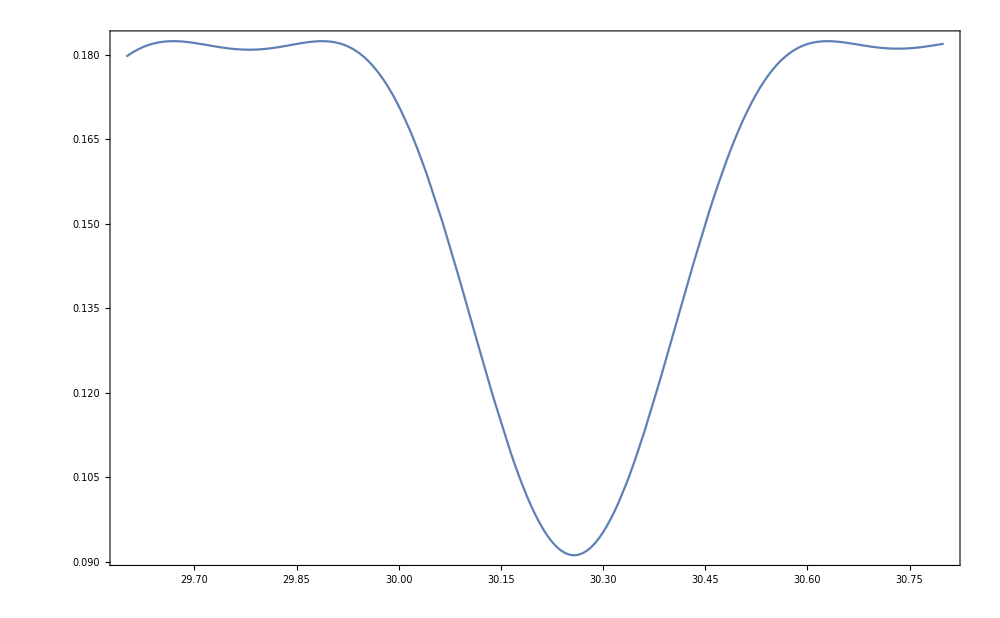

```mathematica
mfhg=Mean[data[[;;,20]]];
pttab=Table[{data[[k]][[-1]]*mfhg/data[[k]][[20]],N[((data[[k]][[27]]-data[[k]][[28]])/(data[[k]][[27]]+data[[k]][[28]]))]},{k,1,maxCy}];
Clear[mult1,mult2,alpha2]
nlm=NonlinearModelFit[pttab,N[(2alpha2-alpha2*Cos[(xx-wo)/mult2]^2Cos[(xx-wo)/mult1]^2)],{alpha2,mult1,mult2},xx,Method->NMinimize]
nlm["ParameterTable"]
Plot[nlm[xx],{xx,29.6,30.8},ImageSize->1000,Frame->True]
```

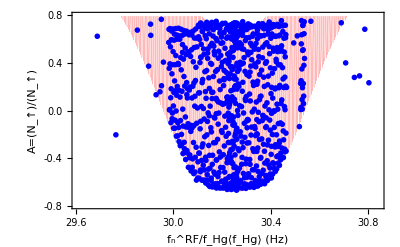

```mathematica
wr=.1;wo=30.25;alpha=.975;finv=50;
pt1[xx_]:=N[(2alpha-(1)alpha*Cos[(xx-wo)*2.7]^2Cos[(xx-wo)*180*Pi]^2)];

Show[{
Plot[(2pt1[w]-3alpha)*((-LogisticSigmoid[(w-30.1)*25]+LogisticSigmoid[(w-30.4)*25])*.315+1),{w,29,31},Frame->True,Axes->False,PlotRange->{{29.61,30.84},{-.79,.79}},FrameLabel->{"f_n^RF/f_Hg⟨f_Hg⟩ (Hz)","A=(N_↑)/(N_↑)"},TicksStyle->Directive[FontSize->40],FrameStyle->Thick,LabelStyle->{28,Black,Bold},FrameTicks->LinTicks,PlotStyle->{{Red,Thickness[.00001]}},ImageSize->{1200},MaxRecursion->10,PlotPoints->250],
ListPlot[pttab,Frame->True,Axes->False,PlotRange->{{29.61,30.84},{-.79,.79}},FrameLabel->{"f_n^RF/f_Hg⟨f_Hg⟩ (Hz)","A=(N_↑)/(N_↑)"},TicksStyle->Directive[FontSize->40],FrameStyle->Thick,LabelStyle->{28,Black,Bold},FrameTicks->LinTicks,PlotStyle->{{Blue,Thick}},ImageSize->{1200},PlotMarkers->{Automatic,Medium}]
}]
```

```mathematica
gamma=1.83247172*100;
b0=1; (*in μT*)
w0=gamma*b0;
w2[w_,w0_,w02_]:=w02(w0-w)^2+w02 (w0-w)^4;
lambda[w_]:=w-w0;
Omega[lambda_,t_]:=1/2 √(lambda^2+(π^2/(4t)^2));
pttu[ww_,t_,tt_]:= 1-N[1/(16(Omega[lambda[ww],t])^4 t^2)Omega[lambda[ww],t]^2 Sin[Omega[lambda[ww],t]×t]^2((2Omega[lambda[ww],t]Cos[Omega[lambda[ww],t]×t]Cos[lambda[ww]×tt/2])-(lambda[ww]Sin[Omega[lambda[ww],t]×t]Sin[lambda[ww]×tt/2]))^2];
pttd[ww_,t_,tt_]:= N[1/(16(Omega[lambda[ww],t])^4 t^2)Omega[lambda[ww],t]^2 Sin[Omega[lambda[ww],t]×t]^2((2Omega[lambda[ww],t]Cos[Omega[lambda[ww],t]×t]Cos[lambda[ww]×tt/2])-(lambda[ww]Sin[Omega[lambda[ww],t]×t]Sin[lambda[ww]×tt/2]))^2];
alpha2[ww_,t_,tt_]:=(pttu[ww,t,tt]-pttd[ww,t,tt])/(pttu[ww,t,tt]+pttd[ww,t,tt]);
```

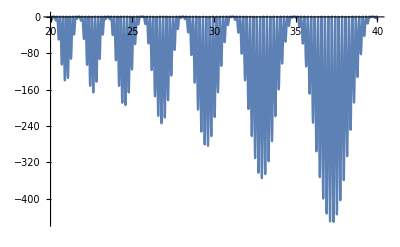

```mathematica
Plot[(64 alpha2[w/(2Pi),Pi/(2 w/(2Pi)),180]-63),{w,20,40},PlotRange->Full]
```

```mathematica
w0/(2Pi)
```

29.1647

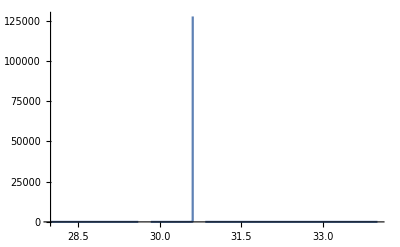

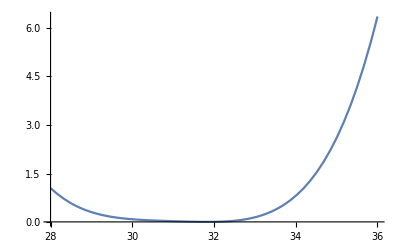

```mathematica
w2[w_,w0_]:=((w0+1)-w)^2+((w0-1)-w)^4;
st=29.61;end=30.84;
Plot[(Piecewise[{{2,w<st},{(LerchPhi[w-29.61,.01,1]+LerchPhi[-w+30.84,.01,1]/10000),(w>st&&w<end)},{2,w>end}}]-1),{w,28,34},PlotRange->Full]
Plot[w2[w,32]/100,{w,28,36},PlotRange->Full]
```

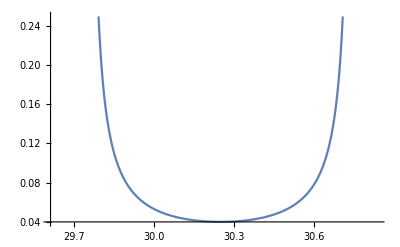

```mathematica
Plot[(LerchPhi[z-(30.25-.5),.01,1]+LerchPhi[-z+(30.25+.5),.01,1])/100,{z,29.61,30.84}]
```

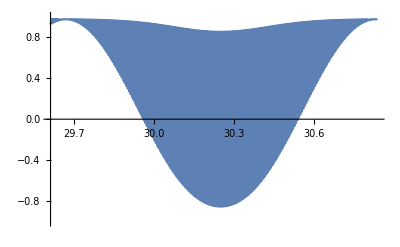

```mathematica
st=30.1;end=30.4;
Plot[(2pt1[w]-3alpha)*((-LogisticSigmoid[(w-30.1)*10]+LogisticSigmoid[(w-30.4)*10])*.2+1),{w,29.61,30.84},PlotRange->{{29.61,30.84},{-1,1}},ImageSize->{1200},MaxRecursion->10,PlotPoints->250]
```

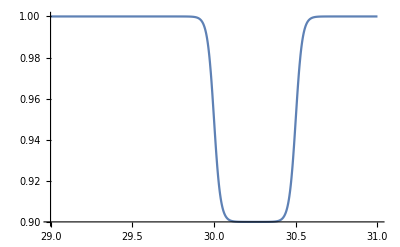

```mathematica
Plot[(-LogisticSigmoid[(x-30)*50]+LogisticSigmoid[(x-30.5)*50])*.1+1,{x,29,31},PlotRange->Full]
```

## T1

FittedModel[0.852394 ⅇ^(-0.000175951 t)]

| Estimate | Standard Error | t-Statistic | P-Value
a0 | 0.852394 | 0.00669673 | 127.285 | 1.76348×10^-25
t1 | 5683.41 | 630.775 | 9.01021 | 1.14741×10^-7

| DF | SS | MS
Model | 2 | 11.5529 | 5.77647
Error | 16 | 0.003026 | 0.000189125
Uncorrected Total | 18 | 11.556 | 
Corrected Total | 17 | 0.0183663 |

χ_T_1^2/ndf =0.287907

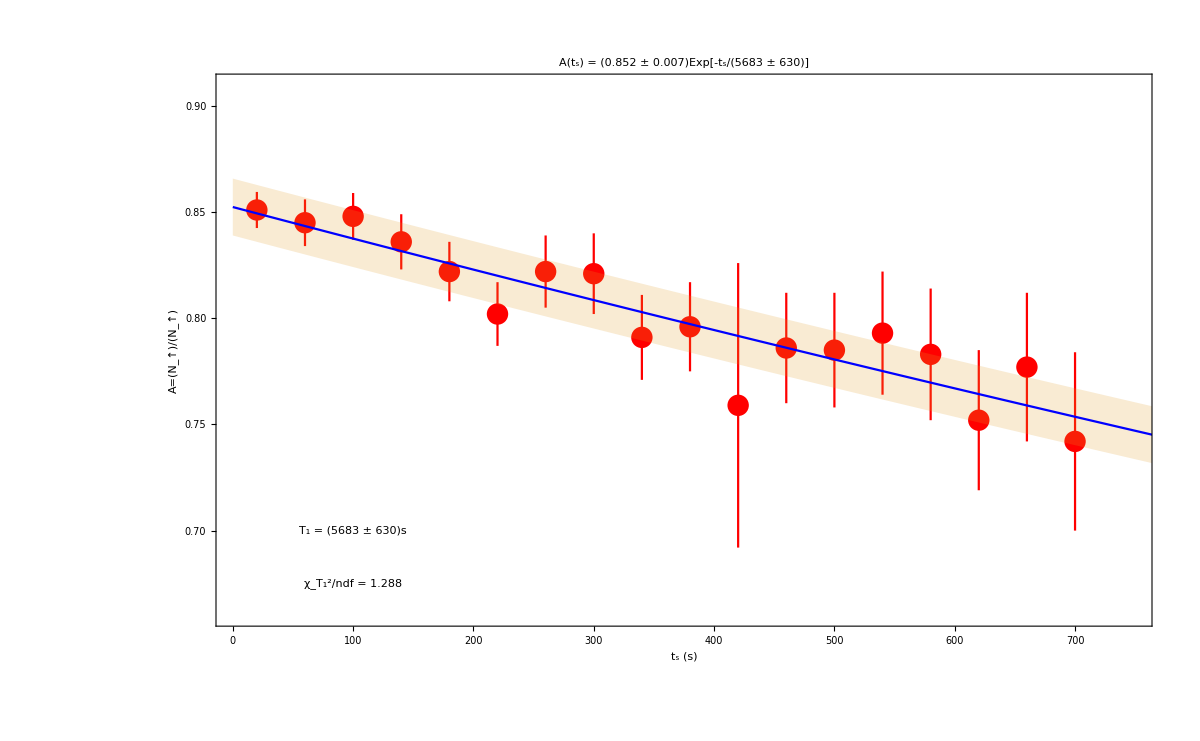

```mathematica
runNum={12443};
i=1;
data1=ReadList[StringJoin[AscDir,"\\","T1","\\",IntegerString[runNum[[i]],10,6],"_Meta3.edm"],metaStructure];
dimdata1=Dimensions[data1][[1]];
pttab=Table[{0,{0,0}},{k,1,dimdata1}];
fttab=Table[{0,0},{k,1,dimdata1}];
a2=Table[0,{k,1,dimdata1}];
For[i=1,i≤dimdata1,i++,
If[i==11,Continue;];
rand=0;
nup=PlusMinus[data1[[i]][[27]]+rand,Sqrt[data1[[i]][[27]]+rand]];
ndown=PlusMinus[data1[[i]][[28]]+rand,Sqrt[data1[[i]][[28]]+rand]];
aa=(nup-ndown)/(nup+ndown);
a2[[i]]=aa;
pttab[[i]]={20+40*(i-1),{aa[[1]],aa[[2]]}};
fttab[[i]]={20+40*(i-1),pttab[[i]][[2]][[1]]};
]
nlm=NonlinearModelFit[fttab,a0 Exp[-t/t1],{a0,t1},t,Method->NMinimize]
nlm["ParameterTable"]
nlm["ANOVATable"]
Print["χ_T_1^2/ndf =",(∑_(i=1)^dimdata1 ((fttab[[i]][[2]]-nlm[fttab[[i]][[1]]])/pttab[[i]][[2]][[2]])^2)/(dimdata1-1)]
Show[{
EDAListPlot[pttab,Frame->True,Axes->False,PlotRange->{{1,749},{.66,.91}},FrameLabel->{"t_s (s)","A=(N_↑)/(N_↑)"},TicksStyle->Directive[FontSize->40],FrameStyle->Thick,LabelStyle->{28,Black,Bold},FrameTicks->LinTicks,ImageSize->1200,PlotStyle->Red,PlotLabel->"A(t_s) = (0.852 ± 0.007)Exp[-t_s/(5683 ± 630)]",
Epilog->{
Text[Style["T_1 = (5683 ± 630)s",FontSize->Large],{100,.7}],
Text[Style["χ_T_1^2/ndf = 1.288",FontSize->Large],{100,.675}]}
],
Plot[{nlm[xx],nlm[xx]-2nlm["ParameterErrors"][[1]],nlm[xx]+2nlm["ParameterErrors"][[1]]},{xx,0,800},PlotStyle->{Blue,None,None},Filling->{2->{3}}]
}]
```

10 | 0.850896
40 | 0.846416
70 | 0.84196
80 | 0.84048
100 | 0.837528
130 | 0.833118
150 | 0.830192
180 | 0.825821
190 | 0.824369
230 | 0.818588
280 | 0.811418
330 | 0.804311

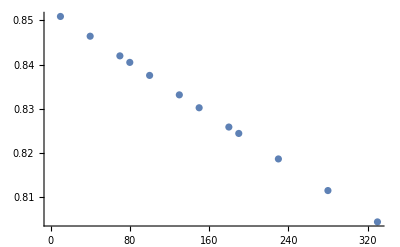

```mathematica
Transpose[{{10,40,70,80,100,130,150,180,190,230,280,330},Map[nlm,{10,40,70,80,100,130,150,180,190,230,280,330}]}]//TableForm
ListPlot[Transpose[{{10,40,70,80,100,130,150,180,190,230,280,330},Map[nlm,{10,40,70,80,100,130,150,180,190,230,280,330}]}]]
```

FittedModel[0.836472 ⅇ^(-0.0000643627 t)]

| Estimate | Standard Error | t-Statistic | P-Value
a0 | 0.836472 | 0.0100449 | 83.2731 | 2.05659×10^-21
t1 | 15536.9 | 7067.48 | 2.19837 | 0.0440321

| DF | SS | MS
Model | 2 | 11.3654 | 5.68272
Error | 15 | 0.00661882 | 0.000441254
Uncorrected Total | 17 | 11.3721 | 
Corrected Total | 16 | 0.00872599 |

χ_T_1^2/ndf =1.04456

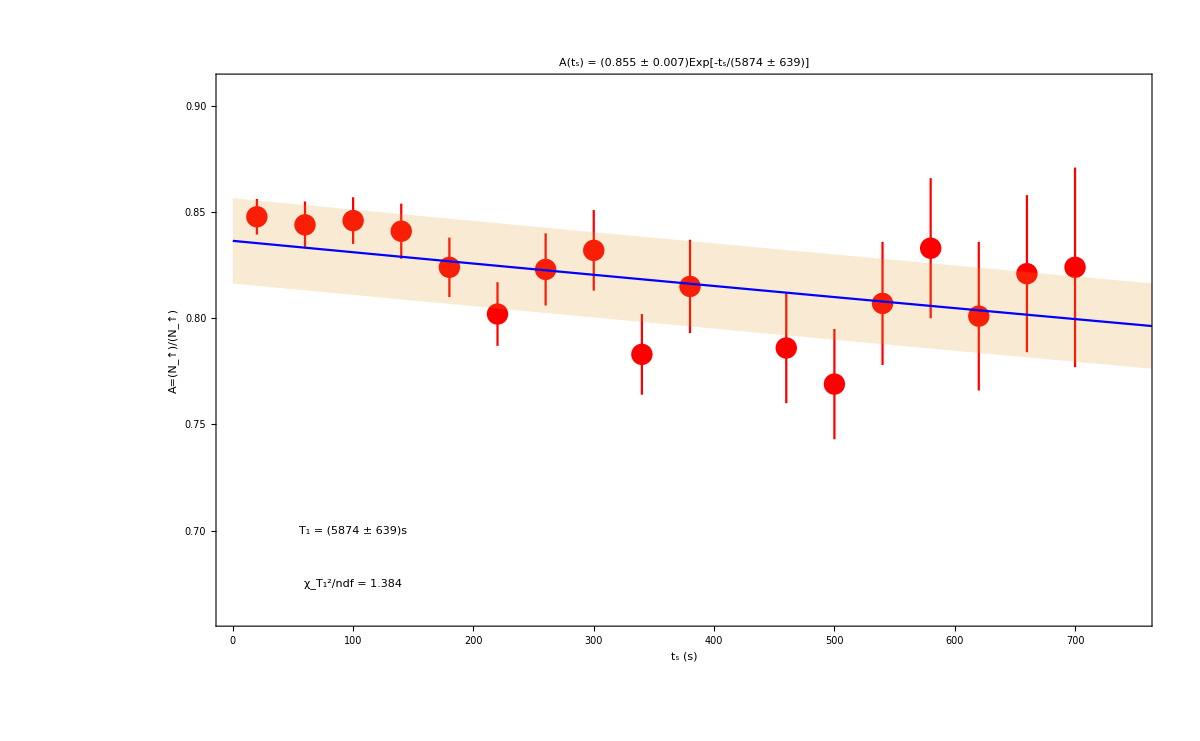

```mathematica
runNum={12443};
i=1;
data1=ReadList[StringJoin[AscDir,"\\","T1","\\",IntegerString[runNum[[i]],10,6],"_Meta3.edm"],metaStructure];
dimdata1=Dimensions[data1][[1]];
pttab=Table[{0,{0,0}},{k,1,dimdata1}];
fttab=Table[{0,0},{k,1,dimdata1}];
For[i=1,i≤dimdata1,i++,
rand=-RandomInteger[{-50,50}];
nup=PlusMinus[data1[[i]][[27]]+rand,Sqrt[data1[[i]][[27]]+rand]];
ndown=PlusMinus[data1[[i]][[28]]+rand,Sqrt[data1[[i]][[28]]+rand]];
aa=(nup-ndown)/(nup+ndown);
pttab[[i]]={20+40*(i-1),{aa[[1]],aa[[2]]}};
fttab[[i]]={20+40*(i-1),pttab[[i]][[2]][[1]]};
]
pttab=Delete[pttab,11];
fttab=Delete[fttab,11];
nlm=NonlinearModelFit[fttab,a0 Exp[-t/t1],{a0,t1},t,Method->NMinimize]
nlm["ParameterTable"]
nlm["ANOVATable"]
Print["χ_T_1^2/ndf =",(∑_(i=1)^(dimdata1-1) ((fttab[[i]][[2]]-nlm[fttab[[i]][[1]]])/pttab[[i]][[2]][[2]])^2)/(dimdata1-2)]
Show[{
EDAListPlot[pttab,Frame->True,Axes->False,PlotRange->{{1,749},{.66,.91}},FrameLabel->{"t_s (s)","A=(N_↑)/(N_↑)"},TicksStyle->Directive[FontSize->40],FrameStyle->Thick,LabelStyle->{28,Black,Bold},FrameTicks->LinTicks,ImageSize->1200,PlotStyle->Red,PlotLabel->"A(t_s) = (0.855 ± 0.007)Exp[-t_s/(5874 ± 639)]",
Epilog->{
Text[Style["T_1 = (5874 ± 639)s",FontSize->Large],{100,.7}],
Text[Style["χ_T_1^2/ndf = 1.384",FontSize->Large],{100,.675}]}
],
Plot[{nlm[xx],nlm[xx]-2nlm["ParameterErrors"][[1]],nlm[xx]+2nlm["ParameterErrors"][[1]]},{xx,0,800},PlotStyle->{Blue,None,None},Filling->{2->{3}}]
}]
```

## T2

FittedModel[0.856123 ⅇ^(-0.000640507 t)]

| Estimate | Standard Error | t-Statistic | P-Value
a0 | 0.856123 | 0.00167904 | 509.889 | 3.27371×10^-33
t1 | 1561.26 | 13.6918 | 114.029 | 1.85605×10^-23

| DF | SS | MS
Model | 2 | 8.31696 | 4.15848
Error | 15 | 0.000145563 | 9.70421×10^-6
Uncorrected Total | 17 | 8.3171 | 
Corrected Total | 16 | 0.128569 |

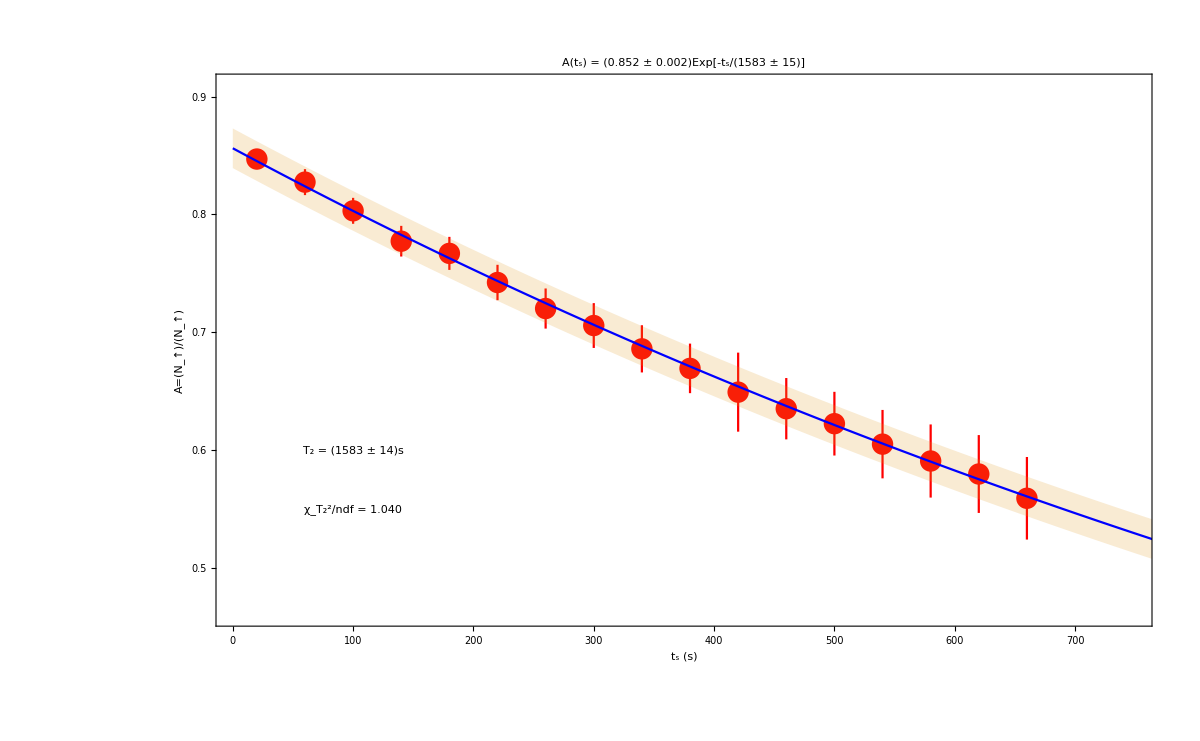

```mathematica
For[i=1,i≤dimdata1,i++,
rand=RandomReal[0.01];
pttab[[i]]={20+40*(i-1),{0.85Exp[-(20+40*(i-1))/1560]+rand,a2[[i]][[2]]}};
fttab[[i]]={20+40*(i-1),pttab[[i]][[2]][[1]]};
If[i==11,pttab[[i]][[2]]={0.85Exp[-(20+40*(i-1))/1560],a2[[i]][[2]]/2};];
]
nlm=NonlinearModelFit[fttab,a0 Exp[-t/t1],{a0,t1},t,Method->NMinimize]
nlm["ParameterTable"]
nlm["ANOVATable"]
Print["χ_T_1^2/ndf =",(∑_(i=1)^dimdata1 ((fttab[[i]][[2]]-nlm[fttab[[i]][[1]]])/pttab[[i]][[2]][[2]])^2)/(dimdata1-1)]
Show[{
EDAListPlot[pttab,Frame->True,Axes->False,PlotRange->{{1,749},{.46,.91}},FrameLabel->{"t_s (s)","A=(N_↑)/(N_↑)"},TicksStyle->Directive[FontSize->40],FrameStyle->Thick,LabelStyle->{28,Black,Bold},FrameTicks->LinTicks,ImageSize->1200,PlotStyle->Red,PlotLabel->"A(t_s) = (0.852 ± 0.002)Exp[-t_s/(1583 ± 15)]",
Epilog->{
Text[Style["T_2 = (1583 ± 14)s",FontSize->Large],{100,.6}],
Text[Style["χ_T_2^2/ndf = 1.040",FontSize->Large],{100,.55}]}
],
Plot[{nlm[xx],nlm[xx]-10nlm["ParameterErrors"][[1]],nlm[xx]+10nlm["ParameterErrors"][[1]]},{xx,0,800},PlotStyle->{Blue,None,None},Filling->{2->{3}}]
}]
```

## Hg/n RF Amplitude

FittedModel[0.841194-7.83144 (-1.42838+x)^2]

| Estimate | Standard Error | t-Statistic | P-Value
a0 | 0.841194 | 0.000825182 | 1019.4 | 9.14259×10^-74
a1 | -7.83144 | 0.184733 | -42.3934 | 1.08593×10^-29
ax | 1.42838 | 0.0011295 | 1264.62 | 9.2375×10^-77

| DF | SS | MS
Model | 3 | 23.7376 | 7.91253
Error | 32 | 0.000541121 | 0.00001691
Uncorrected Total | 35 | 23.7381 | 
Corrected Total | 34 | 0.0469318 |

χ_(n - RF)^2/ndf =0.187647

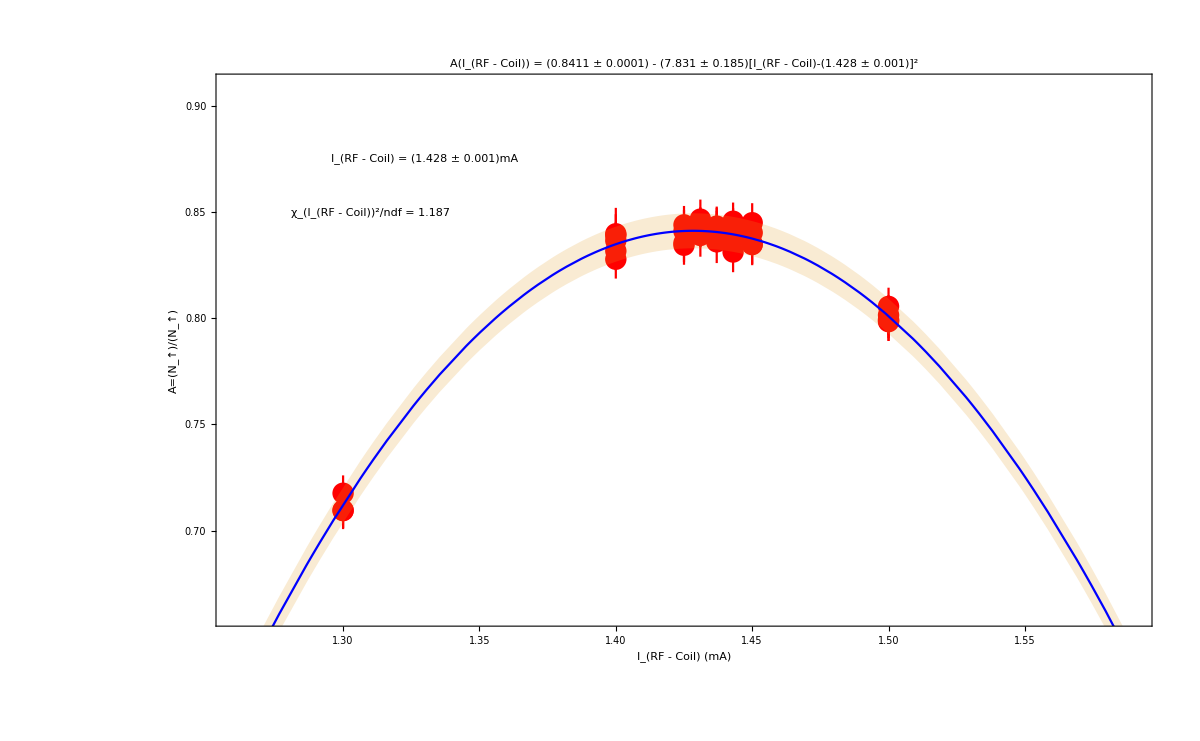

```mathematica
runNum={11013};
i=1;
data1=ReadList[StringJoin[AscDir,"\\","RFAmp","\\",IntegerString[runNum[[i]],10,6],"_Meta3.edm"],metaStructure];
dimdata1=Dimensions[data1][[1]];
pttabn=Table[{0,{0,0}},{k,1,dimdata1}];
fttabn=Table[{0,0},{k,1,dimdata1}];
pttabhg=Table[{0,{0,0}},{k,1,dimdata1}];
fttabhg=Table[{0,0},{k,1,dimdata1}];
For[i=1,i≤dimdata1,i++,
nup=PlusMinus[data1[[i]][[27]],Sqrt[data1[[i]][[27]]]];
ndown=PlusMinus[data1[[i]][[28]],Sqrt[data1[[i]][[28]]]];
aa=(nup-ndown)/(nup+ndown);
pttabn[[i]]={data1[[i]][[-3]]/1000,{aa[[1]],aa[[2]]}};
fttabn[[i]]={data1[[i]][[-3]]/1000,aa[[1]]};
pttabhg[[i]]={data1[[i]][[-8]]/1000,{aa[[1]],aa[[2]]}};
fttabhg[[i]]={data1[[i]][[-8]]/1000,aa[[1]]};
]
nlmn=NonlinearModelFit[fttabn,a1(x-ax)^2+a0,{{a0,.85},{a1,-4},{ax,1.45}},x]
nlmn["ParameterTable"]
nlmn["ANOVATable"]
Print["χ_(n - RF)^2/ndf =",(∑_(i=1)^dimdata1 ((fttabn[[i]][[2]]-nlmn[fttabn[[i]][[1]]])/pttabn[[i]][[2]][[2]])^2)/(dimdata1-1)]
(*nlmhg=NonlinearModelFit[fttabhg,a1(x-ax)^2-a0,{a0,a1,ax},x,Method->NMinimize]
nlmhg["ParameterTable"]
nlmhg["ANOVATable"]
Print["χ_(Hg - RF)^2/ndf =",(∑_(i=1)^dimdata1 ((fttabhg[[i]][[2]]-nlmhg[fttabhg[[i]][[1]]])/pttabhg[[i]][[2]][[2]])^2)/(dimdata1-1)]*)
Show[{
EDAListPlot[pttabn,Frame->True,Axes->False,PlotRange->{{1.26,1.59},{.66,.91}},FrameLabel->{"I_(RF - Coil) (mA)","A=(N_↑)/(N_↑)"},TicksStyle->Directive[FontSize->40],FrameStyle->Thick,LabelStyle->{28,Black,Bold},FrameTicks->LinTicks,ImageSize->1200,PlotStyle->{Red,Blue},PlotLabel->"A(I_(RF - Coil)) = (0.8411 ± 0.0001) - (7.831 ± 0.185)[I_(RF - Coil)-(1.428 ± 0.001)]^2",
Epilog->{
Text[Style["I_(RF - Coil) = (1.428 ± 0.001)mA",FontSize->Large],{1.33,.875}],
Text[Style["χ_(I_(RF - Coil))^2/ndf = 1.187",FontSize->Large],{1.31,.85}]}
],
Plot[{nlmn[xx],nlmn[xx]-10nlmn["ParameterErrors"][[1]],nlmn[xx]+10nlmn["ParameterErrors"][[1]]},{xx,0,2},PlotStyle->{Blue,None,None,Black},Filling->{2->{3}}]
}]
```

## Test

```mathematica
(*
nlm3["ParameterErrors"][[1]];
Epilog->{
Text[Style["χ_(B_↑)^2/ndf = 1.3884",FontSize->Large],{10,.4}],
Text[Style["χ_(B_↑)^2/ndf = 1.7041",FontSize->Large],{10,.3}]};
*)
```